```mathematica
space0symbol0=(x1∨x2∨x3)∧(x2∨x3∨x4)∧(x3∨x4∨x5)∧(x4∨x5∨x6)∧(x5∨x6∨x7)∧(x6∨x7∨x8);
space1symbol0=(x1∨x3∨x5)∧(x2∨x4∨x6)∧(x3∨x5∨x7)∧(x4∨x6∨x8);
space0symbol1=(¬x1∨¬x2∨¬x3)∧(¬x2∨¬x3∨¬x4)∧(¬x3∨¬x4∨¬x5)∧(¬x4∨¬x5∨¬x6)∧(¬x5∨¬x6∨¬x7)∧(¬x6∨¬x7∨¬x8);
space1symbol0=(x1∨x3∨x5)∧(x2∨x4∨x6)∧(x3∨x5∨x7)∧(x4∨x6∨x8);
space1symbol1=(¬x1∨¬x3∨¬x5)∧(¬x2∨¬x4∨¬x6)∧(¬x3∨¬x5∨¬x7)∧(¬x4∨¬x6∨¬x8);
space2symbol0=(x1∨x4∨x7)∧(x2∨x5∨x8);
space2symbol1=(¬x1∨¬x4∨¬x7)∧(¬x2∨¬x5∨¬x8);
```

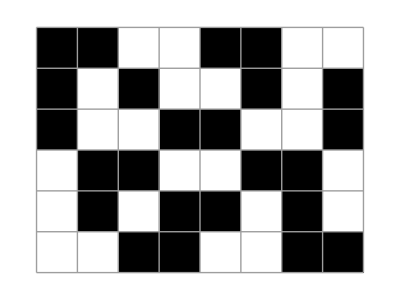

```mathematica
sat[x1,x2,x3,x4,x5,x6,x7,x8,space0symbol0∧space0symbol1∧space1symbol0∧space1symbol1∧space2symbol0∧space2symbol1]//plt
```

got that is beautiful, we can use a sat solver to find these!